### 使用前需加载 yxlllc 开发的 SMSP 编译器

```mathematica
Chor[Cname_,pat_]:=StringJoin[Cname,"> ", pat, "|"]
ChordText[cp_,col_]:=StringReplace[StringJoin[Table[Chor[cp⟦i,2col-1,x⟧,cp⟦i,2col,x⟧],{i,1,Length[cp]},{x,1,Length[cp⟦i,1⟧]}],"\n\n"],")|"->")"]
```

```mathematica
AlphaChord[cp_]:=Module[{test=
StringJoin[(*"beat=4\nbpm=120\nbase=0\n\n",*)
"[t1] i[Midi[Flute]] v[1]
[t2] i[Midi[Piano]] v[.9]
[t3] i[Midi[Violin]] v[.3] \n\n",
"[t1] |0] ",ChordText[cp,1],
"[t2] |0] ",ChordText[cp,2],
"[t3] |0] ",ChordText[cp,3]
]},
(*Export["ACv0.2.0.txt",test];*)
MusicCreate@SMSPCompile[test,"CChordExtend"->True]
]
```

### 和弦进行库

```mathematica
(* 万能和弦（中国80~90老歌，美国50年代乡村经典） *)
C645={"^C","Am","F","G"};
C625={"^C","Am","^Dm","G"};
C6475={"^C","Am","F","Bd","G"};
(* 流行朋克进行 *)
C564={"^C","G","Am","F"};
(* 卡农进行（黄金八和弦，华语第一用烂） *)
Cn[a_,b_,c_]:={"^C","G","Am",{"G","Em"}⟦a⟧,"F",{"C","Em"}⟦b⟧,{"F","Dm"}⟦c⟧,"G"}; 
CnA={"Am","Em","F","C","Dm","E","Am","Am"};
(* 终止式提前（稻香） *)
CnC={"^C","G","Am","Em","F","G","^C","^C"};
(* 连续四度进行（4536251，华语第二用烂） *)
Qd[a_,b_]:={"F","G","Em","Am",{"F","Dm"}⟦a⟧,"G","^C",{"^C","^C7"}⟦b⟧}; 
QdA={"Am","G","^C","F","Bd","E","Am"}; 
(* 纯三骨架朋克 *)
CFG={"^C","F","G","^C","^C","G","F","^C","^C","G","F","G","^C","F","^C","G"};
(* 根音连续下行（有一种爱叫做放手） *)
Adown[a_,b_]:={"Am","G","F",{"Em","E"}⟦a⟧,"^Dm","^C",{"Bd","^Dm","F"}⟦b⟧,"E"};
(* 调性模糊（21 guns，菊次郎的夏天） *)
A6145={"Am","^C","F","G"};
A6415={"Am","F","^C","G"};
(* 烂大街起头 *)
AE={"Am","Em"};
(* 童年，夜空中最亮的星 *)
E152={"Em7","C","G","D"};

(* 重复 *)
r[s_,time_]:=Flatten[Table[s,{time}]]
(* 倍乘 *)
x[s_,time_]:=Flatten[Table[r[s⟦i⟧,time],{i,1,Length[s]}]]
```

### 快速试听

格式为：{和弦进行，主旋律种子，和弦进行，和弦表现型，和弦进行，Bass节奏型}

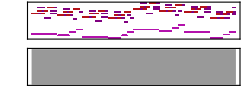

```mathematica
AlphaChord[{
{Adown[1,1],
r[{"a b_ a_ b_ c"},8],
Adown[1,1],
{"a s !c s","a s a_ !c_ c_ b_",
"a s !c s","a s a_ !c_ b_ a_",
"a s !c s","a s a_ !c_ a_ c_",
"a s !c s","a s a_ s_ c_ u_"},
Adown[1,1],
r[{"!!a---","!!a- !!b !!c"},4]}
}]
```

### 节奏型库

TODO

### 常用点缀库

TODO

### 从种子序列映射主旋律

以 8 个小节为一个和弦进行，要生成几个

```mathematica
len=2;
```

随机插零

```mathematica
f[n_]:=If[Mod[n,7]<5,{"!c","a","b","c","^a","^b"}⟦Mod[n,6]+1⟧,"0"]
g=Partition[f/@RealDigits[π,10,8*8*len]⟦1⟧,8];
```

统一前半句

```mathematica
Table[g⟦4n+2,1;;4⟧=g⟦4n+1,1;;4⟧,{n,0,2len-1}];
```

```mathematica
gt=Table[StringJoin[Riffle[Join[g⟦i⟧,{""}],"_ "]],{i,1,Length[g]}];
```

第4小节长音

```mathematica
Table[gt⟦4n⟧=StringJoin[Riffle[g⟦4n,1;;4⟧,"_ "],"_ ",g⟦4n,5⟧," ",g⟦4n,6⟧," "],{n,1,len}];
```

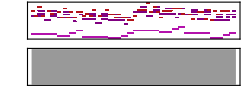

```mathematica
AlphaChord[{
{Adown[1,1],
gt,
Adown[1,1],
{"a s !c s","a s a_ !c_ c_ b_",
"a s !c s","a s a_ !c_ b_ a_",
"a s !c s","a s a_ !c_ a_ c_",
"a s !c s","a s a_ s_ c_ u_"},
Adown[1,1],
r[{"!!a---","!!a- !!b !!c"},4]}
}]
```